# fiber tests

```mathematica
constsdir="..\\constants\\";
imagedir=FileNameJoin[{NotebookDirectory[],"\\images\\"}];
solndir=FileNameJoin[{NotebookDirectory[],"\\solns\\"}];
Do[
AppendTo[$Path, FileNameJoin[{NotebookDirectory[],dir}]];,
{dir,{constsdir,imagedir,solndir}}
]
SetDirectory[NotebookDirectory[]];
<<"physconsts.m"
<<"rbconsts.m"
conj[z_]:=z/.{ⅈ-> -ⅈ,-ⅈ->ⅈ};
SetOptions[Plot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 16],ImageSize->Medium];
SetOptions[ListPlot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 14],ImageSize->Medium];
```

## iXBlue - PZ @ 840 nm

```mathematica
angles = Range[0,180,10];
power = {452,446,330,180,38,2.17,75.7,233,400,480,450,340,176,42.6,68.5,73.2,212.3,370.6,465};
```

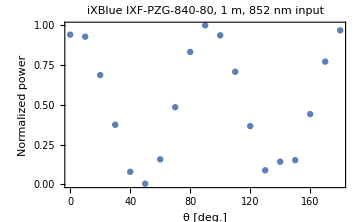

```mathematica
plt=ListPlot[Transpose@{angles,power/Max[power]},FrameLabel->{"θ [deg.]","Normalized power"},PlotLabel->"iXBlue IXF-PZG-840-80, 1 m, 852 nm input"]
```

```mathematica
Export["IXF-PZG-840-80_fiber_1m_constrast_202100806.png",plt]
```

IXF-PZG-840-80_fiber_1m_constrast_202100806.png

```mathematica
max = Max[power];
min = Min[power];
(max-min)/(max+min)
```

0.990999

```mathematica
min/max
```

0.00452083